Subintervall: {1,1000}

Genutzte Eigenwerte (N): 1000

Erster Eigenwert im Fit: 5.30468

Letzter Eigenwert im Fit: 287.289

--- 3-Term-Weyl-Fit mit Ridge-Regularisierung (Python-kompatibel) ---

Fenster (k/N): {0.2,0.9}

A0 (Ridge): 0.2346719091

A1 (Ridge): -0.4758502978

A2 (Ridge): -0.3691692792

Volumen (aus Spektrum, 3-Term): 13.8967

Volumen (geometrisch):          14.4513

Relativer Fehler:               0.038378

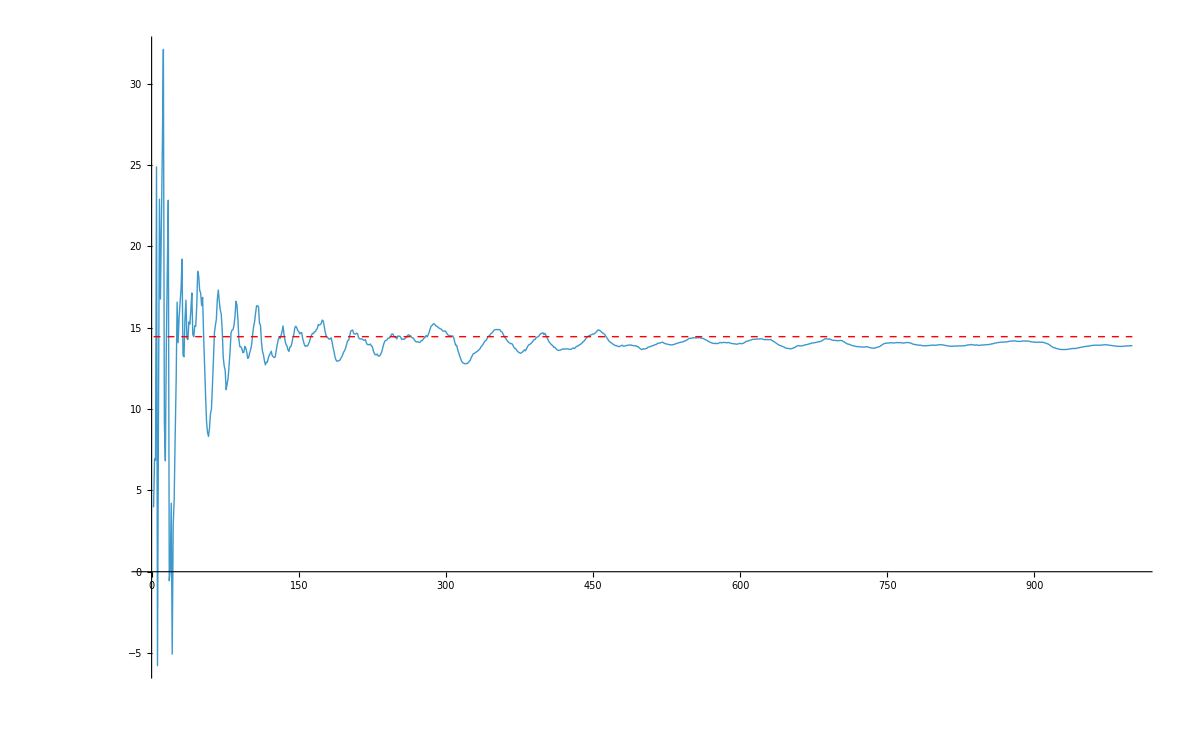

```mathematica
Clear["Global`*"];
Needs["NDSolve`FEM`"];

eigenvalueFilePath="C:\\Users\\sulta\\git\\cone-operator-lab\\mathematica\\ellipsoid_eigs_a1_b1.5_c2.3_arnoldi-1000.txt";
eigsIndexRange={1,1000};

(* Eigenwerte einlesen *)
targetEigenvaluesRaw=Import[eigenvalueFilePath,"Table"]//Flatten;
targetEigenvaluesSorted=Sort[targetEigenvaluesRaw];
targetEigenvalues=targetEigenvaluesSorted[[eigsIndexRange[[1]];;eigsIndexRange[[2]]]];
numEigs=Length[targetEigenvalues];

Print["Subintervall: ",eigsIndexRange];
Print["Genutzte Eigenwerte (N): ",numEigs];
Print["Erster Eigenwert im Fit: ",First[targetEigenvalues]];
Print["Letzter Eigenwert im Fit: ",Last[targetEigenvalues]];

(* Hauptfenster für finale Ergebnisse *)
fitFracRangeMain={0.2,0.9};
lambdaReg=10^-6;

(* eigs:Liste der Eigenwerte λ_k (sortiert) fracRange:[r1,r2] mit
0<r1<r2≤1 für k-Bereich k/N lambdaReg:Regularisierungsstärke (Tikhonov) auf Einheitsmatrix *)
fitFracRangeMain={0.2,0.9};
lambdaReg=10^-6;
fitWeyl3Ridge[eigs_List,fracRange_:{0.2,0.9},lambdaReg_:10^-6]:=Module[
{vals=N@eigs,n,r1,r2,kMin,kMax,lamVals,kVals,X,ATA,ATy,reg,coeffs},
n=Length[vals];
{r1,r2}=N@fracRange;
kMin=Ceiling[r1 n];
kMax=Floor[r2 n];
lamVals=vals[[kMin;;kMax]];
kVals=N@Range[kMin,kMax];
(* Design-Matrix:Spalten={λ^(3/2),λ,√λ} *)
X=Transpose@{lamVals^(3/2),lamVals,Sqrt[lamVals]};
ATA=Transpose[X].X;
ATy=Transpose[X].kVals;
(* NEU:Ridge-Regularisierung wie in Python:(ATA+α I) *)
reg=lambdaReg IdentityMatrix[Length[ATA]];
coeffs=LinearSolve[ATA+reg,ATy];
coeffs
];

(* Volumen aus spektralem A0-Term *)
(* Fit auf festem "ehrlichen" Fenster {0.2,0.9} *)
{A0fit,A1fit,A2fit}=fitWeyl3Ridge[targetEigenvalues,fitFracRangeMain,lambdaReg];
volSpec=6 Pi^2 A0fit;

(* Wahre Achsen *)
trueA=1.0;
trueB=1.5;
trueC=2.3;
volTrue=4 Pi/3 trueA trueB trueC;

Print[""];
Print["--- 3-Term-Weyl-Fit mit Ridge-Regularisierung (Python-kompatibel) ---"];
Print["Fenster (k/N): ",fitFracRangeMain];
Print["A0 (Ridge): ",NumberForm[A0fit,10]];
Print["A1 (Ridge): ",NumberForm[A1fit,10]];
Print["A2 (Ridge): ",NumberForm[A2fit,10]];
Print["Volumen (aus Spektrum, 3-Term): ",NumberForm[volSpec,6]];
Print["Volumen (geometrisch):          ",NumberForm[volTrue,6]];
Print["Relativer Fehler:               ",NumberForm[Abs[volSpec-volTrue]/volTrue,6]];

maxN=Length[targetEigenvalues];
volConvData=Table[
Module[
{eigsSub,coeffs,A0,vol},
eigsSub=targetEigenvalues[[1;;m]];
coeffs=fitWeyl3Ridge[eigsSub,fitFracRangeMain,lambdaReg];
A0=coeffs[[1]];
vol=6 Pi^2 A0;
{m,vol}
],
{m,2,maxN}
];

convPlot=Show[
{
ListLinePlot[volConvData,PlotRange->All,PlotStyle->Thick],
Plot[volTrue,{x,2,maxN},PlotStyle->{Red,Dashed,Thick}]
},
PlotLegends->Placed[
{Style["V_N aus Spektrum",12],Style["Wahres Volumen V_true",12]},
{0.8,0.2}
],
ImageSize->1200
];

convPlot
```